## SSANetwork-example.nb SSANetwork, X2SSANetwork example

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<xSSAlite.m;
<<xlr8r.m;
<<Cellzilla2D.m
```

xSSAlite 1.3.2 loaded Thu-15-Jun-2017-09:21:20 using Mathematica 11.1.1 for Mac OS X x86 (64-bit) (April 27, 2017)(11..1)

xCellerator 0.95 (28-Feb-2014) loaded Thu 15 Jun 2017 09:21:20
using Mathematica 11.1.1 for Mac OS X x86 (64-bit) (April 27, 2017) (Version 11.1, Release 1)

Cellzilla2D (3.0.51f (14 June 2017)) loaded Thu 15 Jun 2017 09:21:20
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

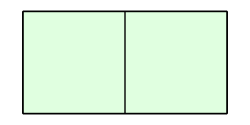

```mathematica
w=TemplateRectangular[2,1];
ShowTissue[w,ImageSize->250]
```

## Define the Cellerator Network

```mathematica
net={{Overscript[S⇄P, X],a,d,k,k4}, {P-> ∅,k1}, {∅⇄S,k2,k3}};
```

```mathematica
myparameters={a-> 10, d-> 0, k-> 1,k1-> 1, k2-> 1, k3-> 1,k4-> 0};
```

```mathematica
singleic = {  S-> 2500, X-> 10, P-> 0};
```

```mathematica
ODE[net]
```

{P'[t]==-k1 P[t]-k4 P[t] X[t]+k Bind[S,X][t],S'[t]==k2-k3 S[t]-a S[t] X[t]+d Bind[S,X][t],X'[t]==-k4 P[t] X[t]-a S[t] X[t]+d Bind[S,X][t]+k Bind[S,X][t],Bind[S,X]'[t]==k4 P[t] X[t]+a S[t] X[t]-d Bind[S,X][t]-k Bind[S,X][t]}

## Run a Deterministic Simulation on a Single Network

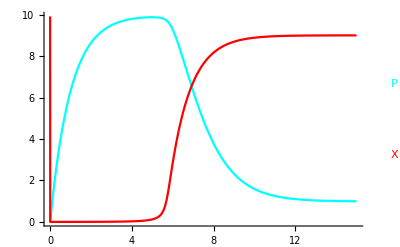

```mathematica
SingleCellDeterministicSimulation=run[net, "Parameters"-> myparameters, "IC"-> singleic, "TimeSpan"-> 15];
dsimplot=runPlot[SingleCellDeterministicSimulation, { P,X}]
```

## Run a stochastic simulation on a single network

```mathematica
sNet=XLR8RtoSSA[net]
```

{{S+X→S⋄X,a},{S⋄X→S+X,d},{S⋄X→P+X,k},{P+X→S⋄X,k4},{P→∅,k1},{∅→S,k2},{S→∅,k3}}

```mathematica
r=SingleCellStochasticSimulation=SSA[sNet,150, singleic, myparameters];
```

xSSA Exit. 3287 steps.  3286 points sampled.  0.24432 seconds.

```mathematica
pdata = Interpolation[P/.r, InterpolationOrder-> 0]
```

InterpolatingFunction[{{0., 150.041}}, <>]

```mathematica
xdata=Interpolation[X/.r, InterpolationOrder-> 0]
```

InterpolatingFunction[{{0., 150.041}}, <>]

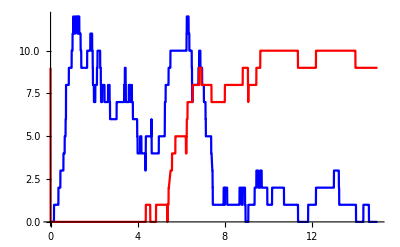

```mathematica
ssimplot=Plot[{pdata[t], xdata[t]}, {t, 0, 15}, PlotStyle-> {Blue,Red}]
```

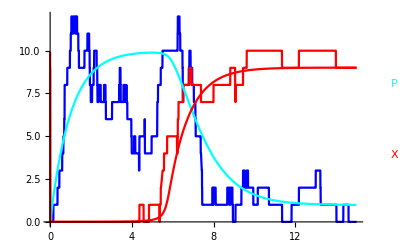

```mathematica
Show[ssimplot,dsimplot]
```

## Generate Multicellular Networks

#### SSA network ⟹ SSA Cellzilla network

```mathematica
s1=SSAtoXLR8R[sNet]
```

{{S+X→S⋄X,a},{S⋄X→S+X,d},{S⋄X→P+X,k},{P+X→S⋄X,k4},{P→∅,k1},{∅→S,k2},{S→∅,k3}}

```mathematica
big1=SSANetwork[sNet, {{X,DX}}, w]
```

2 Cells.

7 internal reactions in each cell.

14 intracellular reactions.

2 diffusion reactions.

16 total reactions.

{{S[1]+X[1]→(S⋄X)[1],a},{(S⋄X)[1]→S[1]+X[1],d},{(S⋄X)[1]→P[1]+X[1],k},{P[1]+X[1]→(S⋄X)[1],k4},{P[1]→∅,k1},{∅→S[1],k2},{S[1]→∅,k3},{S[2]+X[2]→(S⋄X)[2],a},{(S⋄X)[2]→S[2]+X[2],d},{(S⋄X)[2]→P[2]+X[2],k},{P[2]+X[2]→(S⋄X)[2],k4},{P[2]→∅,k1},{∅→S[2],k2},{S[2]→∅,k3},{X[1]→∅,DX},{∅→X[1],DX X[2]},{X[2]→∅,DX},{∅→X[2],DX X[1]}}

#### xlr8r network ⟹ SSA Cellzilla network

```mathematica
big2=X2SSANetwork[net, {{X,DX}}, w]
```

2 Cells.

7 internal reactions in each cell.

14 intracellular reactions.

2 diffusion reactions.

16 total reactions.

{{S[1]+X[1]→Bind[S,X][1],a},{Bind[S,X][1]→S[1]+X[1],d},{Bind[S,X][1]→P[1]+X[1],k},{P[1]+X[1]→Bind[S,X][1],k4},{P[1]→∅,k1},{∅→S[1],k2},{S[1]→∅,k3},{S[2]+X[2]→Bind[S,X][2],a},{Bind[S,X][2]→S[2]+X[2],d},{Bind[S,X][2]→P[2]+X[2],k},{P[2]+X[2]→Bind[S,X][2],k4},{P[2]→∅,k1},{∅→S[2],k2},{S[2]→∅,k3},{X[1]→∅,DX},{∅→X[1],DX X[2]},{X[2]→∅,DX},{∅→X[2],DX X[1]}}

#### The networks are the same

```mathematica
big1==(big2/.{Bind-> Diamond})
```

True

## Do a stochastic simulation

```mathematica
myparameters={a-> 10, d-> 0, k-> 1,k1-> 1, k2-> 1, k3-> 1,k4-> 0, DX-> 1};
```

```mathematica
singleic = {  S-> 2500, X-> 10, P-> 0};
```

```mathematica
theic={S[1]-> 2500, S[2]-> 2500, X[1]-> 10, X[2]-> 0, P[1]-> 0, P[2]-> 0}
```

{S[1]→2500,S[2]→2500,X[1]→10,X[2]→0,P[1]→0,P[2]→0}

```mathematica
bigsim=SSA[big2,15, theic, myparameters,"Mode"-> "Interpolation"]
```

xSSA Exit. 5464 steps.  5463 points sampled.  0.65732 seconds.

{P[1]→InterpolatingFunction[{{0., 14.8109}}, <>],P[2]→InterpolatingFunction[{{0., 14.7818}}, <>],S[1]→InterpolatingFunction[{{0., 14.0682}}, <>],S[2]→InterpolatingFunction[{{0., 13.7928}}, <>],X[1]→InterpolatingFunction[{{0., 14.9886}}, <>],X[2]→InterpolatingFunction[{{0., 15.0113}}, <>],Bind[S,X][1]→InterpolatingFunction[{{0., 14.7548}}, <>],Bind[S,X][2]→InterpolatingFunction[{{0., 14.7818}}, <>]}

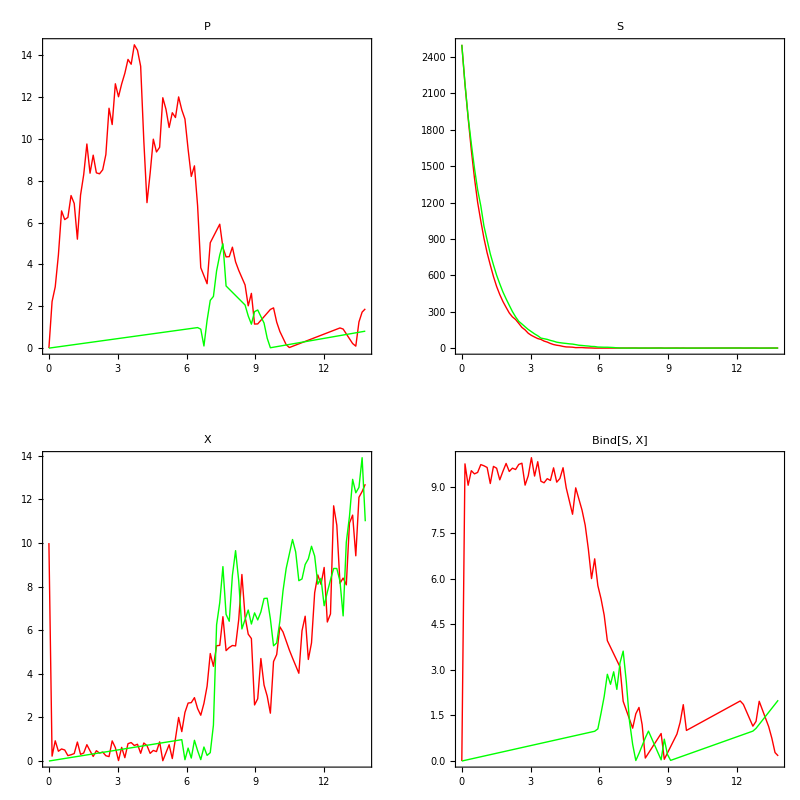

```mathematica
splots=SimPlot[bigsim];
GraphicsGrid[Partition[splots,2]]
```

## Run the “equivalent” deterministic simulation on the tissue

```mathematica
dnet=CelleratorNetwork[w, "Reactions"-> net, "Diffusion"-> {{X,DX}}]
```

2 Cells.

7 internal reactions in each cell.

14 intracellular reactions.

2 diffusion reactions.

16 total reactions.

{{S[1]+X[1]→Bind[S,X][1],a},{Bind[S,X][1]→S[1]+X[1],d},{Bind[S,X][1]→P[1]+X[1],k},{P[1]+X[1]→Bind[S,X][1],k4},{P[1]→∅,k1},{∅→S[1],k2},{S[1]→∅,k3},{S[2]+X[2]→Bind[S,X][2],a},{Bind[S,X][2]→S[2]+X[2],d},{Bind[S,X][2]→P[2]+X[2],k},{P[2]+X[2]→Bind[S,X][2],k4},{P[2]→∅,k1},{∅→S[2],k2},{S[2]→∅,k3},{X[1]⇄∅,DX,DX X[2][t]},{X[2]⇄∅,DX,DX X[1][t]}}

```mathematica
dsim=RunSim[dnet, myparameters,theic, {0,15}]
```

{P[1]→InterpolatingFunction[{{0., 15.}}, <>],P[2]→InterpolatingFunction[{{0., 15.}}, <>],S[1]→InterpolatingFunction[{{0., 15.}}, <>],S[2]→InterpolatingFunction[{{0., 15.}}, <>],X[1]→InterpolatingFunction[{{0., 15.}}, <>],X[2]→InterpolatingFunction[{{0., 15.}}, <>],Bind[S,X][1]→InterpolatingFunction[{{0., 15.}}, <>],Bind[S,X][2]→InterpolatingFunction[{{0., 15.}}, <>]}

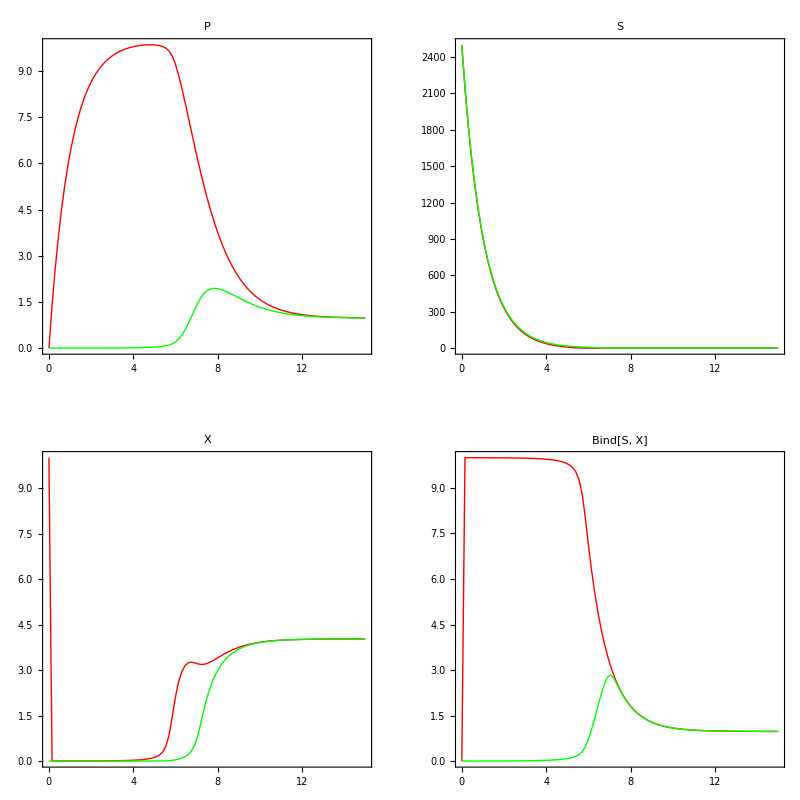

```mathematica
dPlots=SimPlot[dsim];
GraphicsGrid[Partition[dPlots,2]]
```

## Compare Deterministic and Stochastic Plots

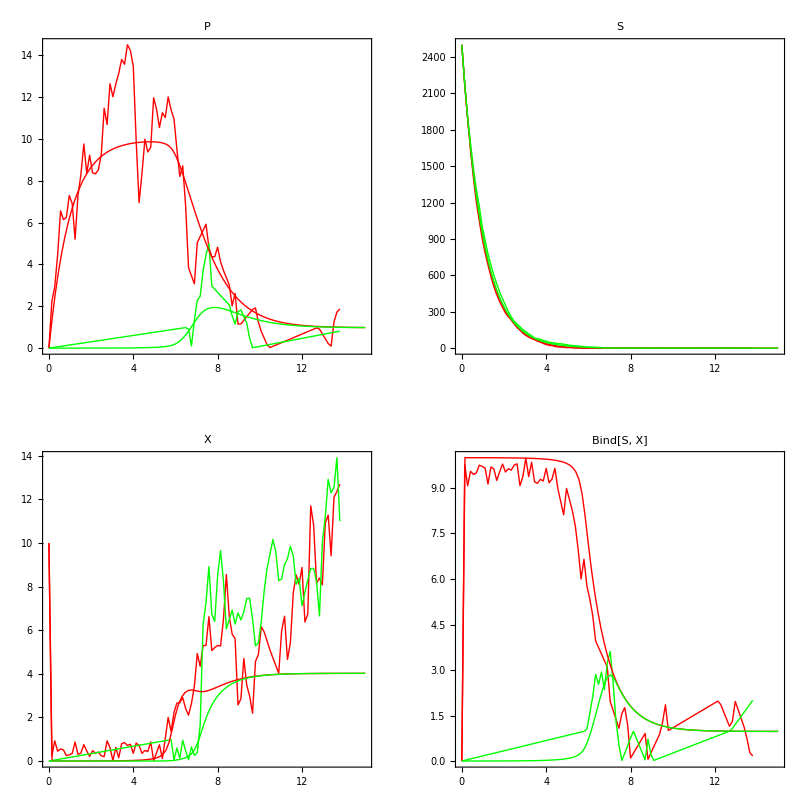

```mathematica
someplots=Show[splots[[#]], dPlots[[#]]]&/@{1,2,3,4};
GraphicsGrid[Partition[someplots,2]]
```